# Ideas for Resource Functions

## different ideas for functions to add to the function repository

Peter Burbery

## Prime Factorization

### Enter subsection title here

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
∫xⅆx+√z
```

x^2/2+√z

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

## Prime Factorization

```mathematica
ResourceSearch["Prime"]
```

```mathematica
CenterDot@@MapApply[Superscript,FactorInteger[201!]]
```

2^197·3^98·5^49·7^32·11^19·13^16·17^11·19^10·23^8·29^6·31^6·37^5·41^4·43^4·47^4·53^3·59^3·61^3·67^3·71^2·73^2·79^2·83^2·89^2·97^2·101^1·103^1·107^1·109^1·113^1·127^1·131^1·137^1·139^1·149^1·151^1·157^1·163^1·167^1·173^1·179^1·181^1·191^1·193^1·197^1·199^1

### Definition

```mathematica
PrimeFactorization[integer_?IntegerQ]:=CenterDot@@MapApply[Superscript,FactorInteger[integer]]
```

### Documentation

Find the prime factorization of 2022:

```mathematica
PrimeFactorization[2022]
```

2^1·3^1·337^1

Find the prime factorization of a large random number:

```mathematica
PrimeFactorization[RandomInteger[10^12]]
```

2^1·95261^1·4854989^1

Find the prime factorization of the factorial of a large number

```mathematica
PrimeFactorization[2018!]
```

2^2011·3^1004·5^502·7^334·11^200·13^166·17^124·19^111·23^90·29^71·31^67·37^55·41^50·43^47·47^42·53^38·59^34·61^33·67^30·71^28·73^27·79^25·83^24·89^22·97^20·101^19·103^19·107^18·109^18·113^17·127^15·131^15·137^14·139^14·149^13·151^13·157^12·163^12·167^12·173^11·179^11·181^11·191^10·193^10·197^10·199^10·211^9·223^9·227^8·229^8·233^8·239^8·241^8·251^8·257^7·263^7·269^7·271^7·277^7·281^7·283^7·293^6·307^6·311^6·313^6·317^6·331^6·337^5·347^5·349^5·353^5·359^5·367^5·373^5·379^5·383^5·389^5·397^5·401^5·409^4·419^4·421^4·431^4·433^4·439^4·443^4·449^4·457^4·461^4·463^4·467^4·479^4·487^4·491^4·499^4·503^4·509^3·521^3·523^3·541^3·547^3·557^3·563^3·569^3·571^3·577^3·587^3·593^3·599^3·601^3·607^3·613^3·617^3·619^3·631^3·641^3·643^3·647^3·653^3·659^3·661^3·673^2·677^2·683^2·691^2·701^2·709^2·719^2·727^2·733^2·739^2·743^2·751^2·757^2·761^2·769^2·773^2·787^2·797^2·809^2·811^2·821^2·823^2·827^2·829^2·839^2·853^2·857^2·859^2·863^2·877^2·881^2·883^2·887^2·907^2·911^2·919^2·929^2·937^2·941^2·947^2·953^2·967^2·971^2·977^2·983^2·991^2·997^2·1009^2·1013^1·1019^1·1021^1·1031^1·1033^1·1039^1·1049^1·1051^1·1061^1·1063^1·1069^1·1087^1·1091^1·1093^1·1097^1·1103^1·1109^1·1117^1·1123^1·1129^1·1151^1·1153^1·1163^1·1171^1·1181^1·1187^1·1193^1·1201^1·1213^1·1217^1·1223^1·1229^1·1231^1·1237^1·1249^1·1259^1·1277^1·1279^1·1283^1·1289^1·1291^1·1297^1·1301^1·1303^1·1307^1·1319^1·1321^1·1327^1·1361^1·1367^1·1373^1·1381^1·1399^1·1409^1·1423^1·1427^1·1429^1·1433^1·1439^1·1447^1·1451^1·1453^1·1459^1·1471^1·1481^1·1483^1·1487^1·1489^1·1493^1·1499^1·1511^1·1523^1·1531^1·1543^1·1549^1·1553^1·1559^1·1567^1·1571^1·1579^1·1583^1·1597^1·1601^1·1607^1·1609^1·1613^1·1619^1·1621^1·1627^1·1637^1·1657^1·1663^1·1667^1·1669^1·1693^1·1697^1·1699^1·1709^1·1721^1·1723^1·1733^1·1741^1·1747^1·1753^1·1759^1·1777^1·1783^1·1787^1·1789^1·1801^1·1811^1·1823^1·1831^1·1847^1·1861^1·1867^1·1871^1·1873^1·1877^1·1879^1·1889^1·1901^1·1907^1·1913^1·1931^1·1933^1·1949^1·1951^1·1973^1·1979^1·1987^1·1993^1·1997^1·1999^1·2003^1·2011^1·2017^1

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}

## Resource Submissions

```mathematica
ResourceFunction["ResourceSubmissions"][]
```

{ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…]}

## IntegralNumberQ

## ApplyGraphEmbeddings

The graph constructions.

### Complete Graph and K-partite graphs

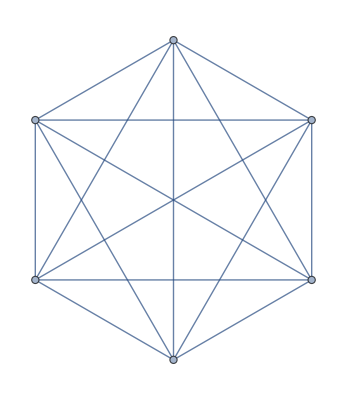

```mathematica
CompleteGraph[6]
```

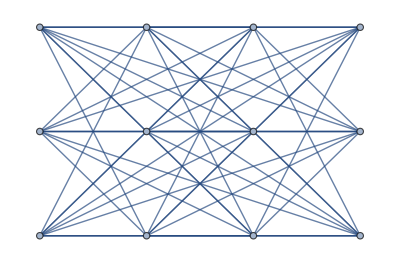

```mathematica
CompleteGraph[{3,3,3,3}]
```

### Buckyball Graph

```mathematica
BuckyballGraph[]
```

-Graphics3D-

```mathematica
BuckyballGraph[3]
```

-Graphics3D-

```mathematica
BuckyballGraph[1,"I"]
```

-Graphics3D-

### Butterfly Graph

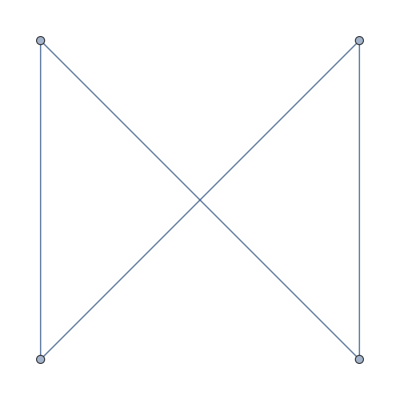

```mathematica
ButterflyGraph[1]
```

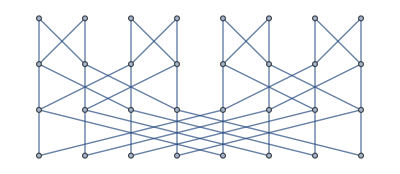

```mathematica
ButterflyGraph[3]
```

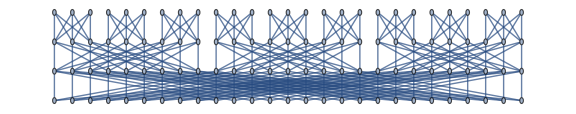

```mathematica
ButterflyGraph[3,3,ImageSize->Large]
```

### Circulant Graph

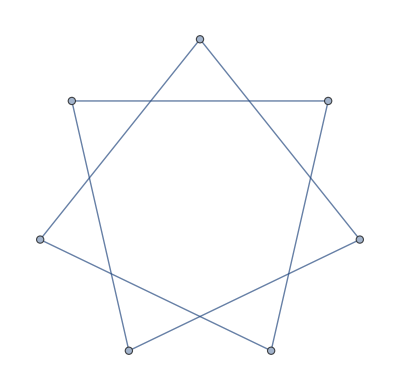

```mathematica
CirculantGraph[7,2]
```

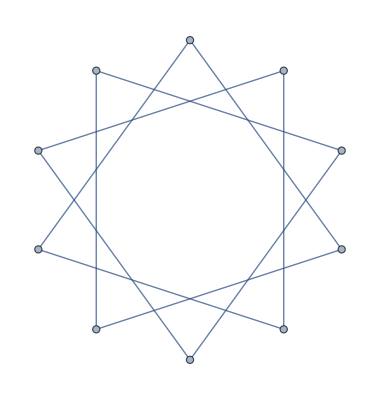

```mathematica
CirculantGraph[10,3]
```

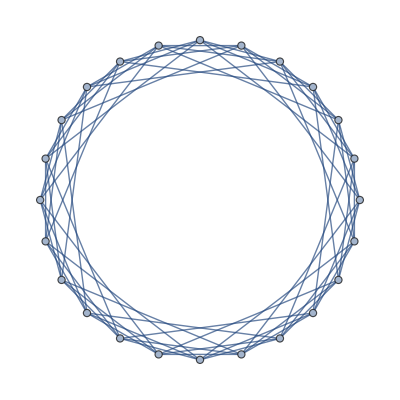

```mathematica
CirculantGraph[24,{2,3,5}]
```

### Complete K-ary tree

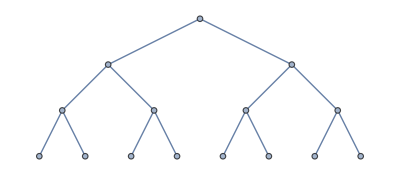

```mathematica
CompleteKaryTree[4]
```

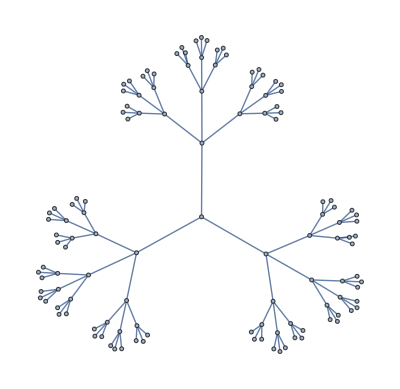

```mathematica
CompleteKaryTree[5,3]
```

### Cycle Graph

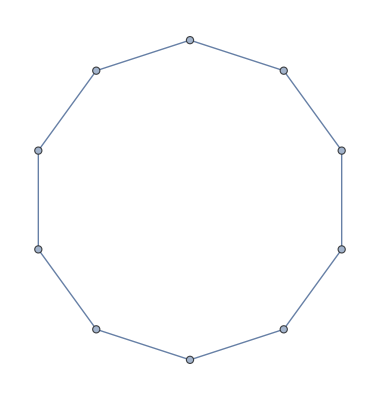

```mathematica
CycleGraph[10]
```

### De Bruijn Graph

```mathematica
DeBruijnGraph[3,2]
```

-Graphics-

```mathematica
DeBruijnGraph[4,3]
```

-Graphics-

```mathematica
DeBruijnGraph[3,2,"Noncyclic"]
```

-Graphics-

```mathematica
DeBruijnGraph[3,2,"LeftShift"]
```

-Graphics-

```mathematica
DeBruijnGraph[3,2,"RightShift"]
```

-Graphics-

### Grid Graph

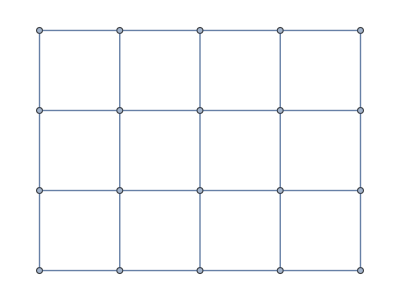

```mathematica
GridGraph[{4,5}]
```

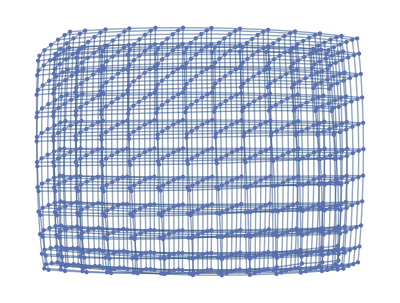

```mathematica
GridGraph[{7,11,13}]
```

```mathematica
Graph3D[GridGraph[{7,11,13}]]
```

-Graphics3D-

### Harary Graph

```mathematica
HararyGraph[5,6]
```

-Graphics-

### Hypercube Graph

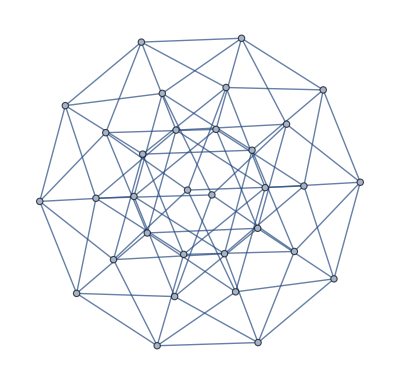

```mathematica
HypercubeGraph[5]
```

```mathematica
BuckyballGraph[GraphLayout->"SpiralEmbedding"]
```

-Graphics3D-

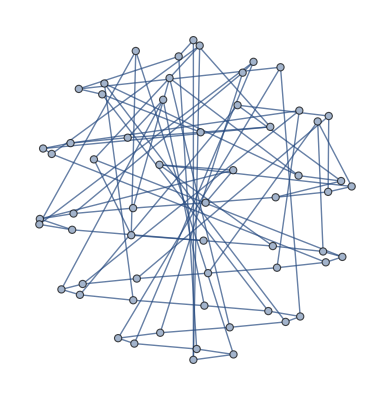

```mathematica
Graph[BuckyballGraph[],GraphLayout->"SpiralEmbedding"]
```

```mathematica
Association[AbsoluteOptions@Graph[BuckyballGraph[],GraphLayout->"SpiralEmbedding"]][VertexCoordinates]
```

{{0.96072,0.},{0.96072,1.99091},{1.00006,1.95716},{1.21097,0.0337442},{1.44038,1.451},{0.869152,1.88967},{0.340311,1.24853},{0.0773326,1.28228},{0.601465,1.92342},{0.981332,0.0674883},{1.20908,1.18105},{1.03712,0.97858},{0.749094,1.21479},{0.00327439,0.877348},{1.47386,1.01232},{0.584602,0.944836},{1.45618,0.708627},{1.9479,1.07981},{0.204771,0.80986},{0.21336,0.911092},{1.00581,1.41725},{0.392187,1.65346},{0.551234,1.38351},{0.0235581,1.31602},{1.42806,0.303697},{0.246162,1.68721},{0.772132,1.61972},{0.194543,1.34977},{1.88199,1.11356},{1.61665,1.1473},{1.23625,1.58598},{1.80103,1.04607},{0.405718,1.72095},{0.812167,1.7547},{0.253194,0.40493},{1.80486,1.51849},{1.02935,0.337442},{0.137667,0.438674},{0.585815,0.371186},{0.270438,0.472418},{0.57329,0.776116},{0.,0.843604},{1.02425,0.742371},{1.3357,1.85593},{1.6269,0.269953},{1.53597,0.236209},{0.592555,0.101232},{1.50409,1.82218},{1.26803,1.78844},{1.18756,0.202465},{1.88991,0.641139},{1.76959,0.674883},{1.78641,0.607395},{1.73581,1.48474},{1.48223,0.573651},{1.05229,0.539906},{1.62136,1.55223},{0.60798,0.506162},{0.491264,0.134977},{0.753861,0.168721}}

```mathematica
GraphEmbedding[BuckyballGraph[],"SpiralEmbedding",2]
```

{{0.96072,0.},{0.96072,1.99091},{1.00006,1.95716},{1.21097,0.0337442},{1.44038,1.451},{0.869152,1.88967},{0.340311,1.24853},{0.0773326,1.28228},{0.601465,1.92342},{0.981332,0.0674883},{1.20908,1.18105},{1.03712,0.97858},{0.749094,1.21479},{0.00327439,0.877348},{1.47386,1.01232},{0.584602,0.944836},{1.45618,0.708627},{1.9479,1.07981},{0.204771,0.80986},{0.21336,0.911092},{1.00581,1.41725},{0.392187,1.65346},{0.551234,1.38351},{0.0235581,1.31602},{1.42806,0.303697},{0.246162,1.68721},{0.772132,1.61972},{0.194543,1.34977},{1.88199,1.11356},{1.61665,1.1473},{1.23625,1.58598},{1.80103,1.04607},{0.405718,1.72095},{0.812167,1.7547},{0.253194,0.40493},{1.80486,1.51849},{1.02935,0.337442},{0.137667,0.438674},{0.585815,0.371186},{0.270438,0.472418},{0.57329,0.776116},{0.,0.843604},{1.02425,0.742371},{1.3357,1.85593},{1.6269,0.269953},{1.53597,0.236209},{0.592555,0.101232},{1.50409,1.82218},{1.26803,1.78844},{1.18756,0.202465},{1.88991,0.641139},{1.76959,0.674883},{1.78641,0.607395},{1.73581,1.48474},{1.48223,0.573651},{1.05229,0.539906},{1.62136,1.55223},{0.60798,0.506162},{0.491264,0.134977},{0.753861,0.168721}}

```mathematica
GraphEmbedding[BuckyballGraph[],"SpiralEmbedding",2]===Association[AbsoluteOptions@Graph[BuckyballGraph[],GraphLayout->"SpiralEmbedding"]][VertexCoordinates]
```

True

```mathematica
GraphEmbedding[BuckyballGraph[],"SpiralEmbedding",3]===Association[AbsoluteOptions@Graph3D[BuckyballGraph[],GraphLayout->"SpiralEmbedding"]][VertexCoordinates]
```

AbsoluteOptions::optnf: Frame is not a known option for Graphics3D.

AbsoluteOptions::optnf: FrameLabel is not a known option for Graphics3D.

AbsoluteOptions::optnf: FrameStyle is not a known option for Graphics3D.

General::stop: Further output of AbsoluteOptions::optnf will be suppressed during this calculation.

True

```mathematica
FullForm@Graph3D[BuckyballGraph[],GraphLayout->"SpiralEmbedding"]
```

Graph[List[1,2,3,4,10,27,39,53,24,33,5,6,7,8,14,30,41,54,28,35,9,11,12,20,31,34,17,43,13,15,16,23,32,36,21,45,18,19,22,51,25,26,29,52,47,48,49,57,50,58,37,38,40,42,55,56,44,46,59,60],List[UndirectedEdge[1,2],UndirectedEdge[1,3],UndirectedEdge[1,4],UndirectedEdge[2,10],UndirectedEdge[2,27],UndirectedEdge[3,39],UndirectedEdge[3,53],UndirectedEdge[4,24],UndirectedEdge[4,33],UndirectedEdge[5,6],UndirectedEdge[5,7],UndirectedEdge[5,8],UndirectedEdge[6,14],UndirectedEdge[6,30],UndirectedEdge[7,41],UndirectedEdge[7,54],UndirectedEdge[8,28],UndirectedEdge[8,35],UndirectedEdge[9,10],UndirectedEdge[9,11],UndirectedEdge[9,12],UndirectedEdge[10,20],UndirectedEdge[11,31],UndirectedEdge[11,34],UndirectedEdge[12,17],UndirectedEdge[12,43],UndirectedEdge[13,14],UndirectedEdge[13,15],UndirectedEdge[13,16],UndirectedEdge[14,23],UndirectedEdge[15,32],UndirectedEdge[15,36],UndirectedEdge[16,21],UndirectedEdge[16,45],UndirectedEdge[17,18],UndirectedEdge[17,19],UndirectedEdge[18,22],UndirectedEdge[18,31],UndirectedEdge[19,21],UndirectedEdge[19,51],UndirectedEdge[20,43],UndirectedEdge[20,53],UndirectedEdge[21,22],UndirectedEdge[22,32],UndirectedEdge[23,45],UndirectedEdge[23,54],UndirectedEdge[24,25],UndirectedEdge[24,26],UndirectedEdge[25,29],UndirectedEdge[25,39],UndirectedEdge[26,28],UndirectedEdge[26,52],UndirectedEdge[27,33],UndirectedEdge[27,34],UndirectedEdge[28,29],UndirectedEdge[29,41],UndirectedEdge[30,35],UndirectedEdge[30,36],UndirectedEdge[31,47],UndirectedEdge[32,48],UndirectedEdge[33,49],UndirectedEdge[34,57],UndirectedEdge[35,50],UndirectedEdge[36,58],UndirectedEdge[37,38],UndirectedEdge[37,39],UndirectedEdge[37,40],UndirectedEdge[38,41],UndirectedEdge[38,42],UndirectedEdge[40,53],UndirectedEdge[40,55],UndirectedEdge[42,54],UndirectedEdge[42,56],UndirectedEdge[43,44],UndirectedEdge[44,51],UndirectedEdge[44,55],UndirectedEdge[45,46],UndirectedEdge[46,51],UndirectedEdge[46,56],UndirectedEdge[47,48],UndirectedEdge[47,57],UndirectedEdge[48,58],UndirectedEdge[49,52],UndirectedEdge[49,59],UndirectedEdge[50,52],UndirectedEdge[50,60],UndirectedEdge[55,56],UndirectedEdge[57,59],UndirectedEdge[58,60],UndirectedEdge[59,60]],List[Rule[GraphLayout,List[Rule["Dimension",3],Rule["VertexLayout","SpiralEmbedding"]]]]]

I need to figure out how to unmerge the submission of ColorGraphEdges and ColorGraphNodes.